## Position from Velocity — Using Associations

## January 21, 2025

Study Sections 4-6 of EIWL3 before working through this notebook.

### Associations

A limitation of Nest and NestList may have already caught your eye: the function you are compounding can only take one argument. Acck! When we are studying particle motion, even in just one dimension, we need at least two values: time and position.

Later, when we are studying the motion of multiple particles in three dimensions, we need positions and velocities for each particle and each of these positions and velocities themselves will have three components!

So there is no way we are going to be able to get by with functions that take and return only a single value. It is therefore essential that we learn how to “hide” multiple values within a single argument.

There are lots of ways to do this, but the clearest, most general way I can think of is to use associations. Here is an association that holds the current time and the current position of a particle moving in one dimension:

```mathematica
state = <|"time"->3600, "position"->10000|>
```

<|time→3600,position→10000|>

This is a single variable that holds two things! In this association, “time” and “position” are keys, and 3600 and 10000 are their respective values.

Of course I could have used a list like this, but it is a little less clear, and the lack of clarity is going to be problematic as we get more general:

```mathematica
stateAsAList ={3600,10000}
```

{3600,10000}

The lack of clarity with lists is that you have to remember that the first element of the list is the time and the second element is the position (or whatever choice you made). The nice thing about associations is that you are forced by the notation to always be clear about which key-value pair of the association you are accessing.

Here is a function that takes an association, adds 1 to the time and 1 to the position and then returns a new association:

```mathematica
addOne[a_]:=(
newTime = a[["time"]]+1;
newPosition = a[["position"]]+1;
<|"time"->newTime, "position"->newPosition|>
)
```

Let’s see if it works:

```mathematica
addOne[<|"time"->3600, "position"->10000|>]
```

<|time→3601,position→10001|>

So we are now able to use Nest and NestList with functions that have multiple values despite only having one argument and one thing returned; the values are hidden in associations.

Using Nest or NestList with a formula (aka a function or a procedure) to apply the formula any number of times is something we already learned to do in the Heads or Tails notebook. Let’s apply addOne five times:

```mathematica
NestList[addOne, <|"time"->3600, "position"->10000|>, 5]
```

{<|time→3600,position→10000|>,<|time→3601,position→10001|>,<|time→3602,position→10002|>,<|time→3603,position→10003|>,<|time→3604,position→10004|>,<|time→3605,position→10005|>}

### The Simplest Formulas

We will use the formulas we derived in the “Position from Velocity — Theory” notebook:

t_2=t_1+Δt

x(t_2)=x(t_1)+v(t_1+Δt/2)·Δt

Now we are going to have to apply this procedure over and over again, so perhaps I should write:

t_(i+1)=t_i+Δt

x(t_(i+1))=x(t_i)+v(t_i+Δt/2)·Δt

If I put in i=10 (as a special case) into these formulas, I get:

t_11=t_10+Δt

x(t_11)=x(t_10)+v(t_10+Δt/2)·Δt

Whatever our initial position is we will call x(t_initial)=x_initial. And our final position at t_final which is x(t_final) — which is what we are trying to find — we could call x_final.

If we do N time steps to get from t_initial to t_final then,

Δt=(t_final-t_initial)/N

or completely equivalently,

N=(t_final-t_initial)/Δt

So the simplest formulas for getting t_(i+1)from t_i and x(t_(i+1))from x(t_i) are going to have to be applied N times to get from t_iniital to t_final.

### Constant Velocity

By far the simplest example is constant velocity. Let’s first write the function that does a constant velocity of 3 and a time step of 0.1, just one time:

```mathematica
move[a_]:=(newTime = a[["time"]]+0.1;
newPosition = a[["position"]]+ 3 * 0.1;
<|"time"->newTime, "position"->newPosition|>
)
```

You have to look very carefully at the theory that we derived and make sure that what we just did was an application of:

t_(i+1)=t_i+Δt

x(t_(i+1))=x(t_i)+v(t_i+Δt/2)·Δt

Then we need to apply this function 15 times to get from 2.0 to 3.5.

We also need to say, where should we start the particle? E.g., what is x_initial? How about at time t_initial=2.0 we say it was at position x_initial=x_0=-2.0?

Alright then, now we apply the function, starting with that initial time and position, 15 times:

```mathematica
allTheAssociations = NestList[move,<|"time"->2.0, "position"->-2.0|>,15];
```

Woo hoo! That was easy. Our result isn’t very graphical, and it isn’t very interesting, because it is constant velocity. Let’s graph it anyway even though it isn’t very interesting. First we graph all the positions:

```mathematica
allThePositions=allTheAssociations[[All,"position"]]
```

{-2.,-1.7,-1.4,-1.1,-0.8,-0.5,-0.2,0.1,0.4,0.7,1.,1.3,1.6,1.9,2.2,2.5}

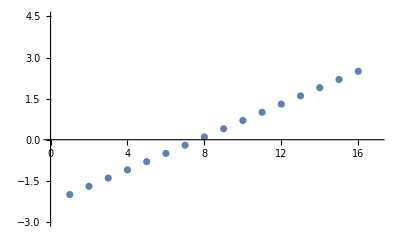

```mathematica
ListPlot[allThePositions, PlotRange->{{0, 17},{-3, 4.5}}]
```

### A Bounce

To make things a little more interesting, how about we do a bounce? We’ll have the particle go at constant velocity of 6 until the time is 3.0, and then bounce and continue at a constant velocity of -6 after that. We’ll make the time steps smaller so that our graph is more detailed:

```mathematica
bounce[a_]:=(
deltaT=0.01;
time = a[["time"]];
position = a[["position"]];
newTime = time+deltaT;
midpointTime =time +deltaT/2;
midpointVelocity = If[midpointTime<3.0,6, -6];
newPosition = position+ midpointVelocity * deltaT;
<|"time"->newTime, "position"->newPosition|>
)
```

We are still going to start at t_initial=2.0.

Notice that because I cranked down the Δt to 0.01, I am going to have to crank up the number of steps to 150, and I am going to suppress the output:

```mathematica
lotsaPositions = NestList[bounce,<|"time"->2.0, "position"->-2.0|>,150];
```

### Displaying the Bounce

```mathematica
allTheBouncePositions = lotsaPositions[[All,"position"]];
```

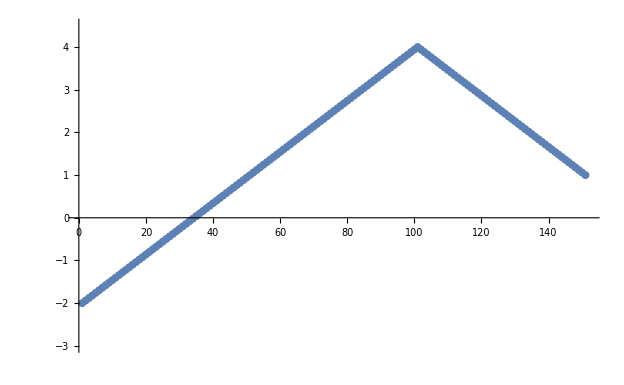

```mathematica
ListPlot[allTheBouncePositions, PlotRange->{{0, 152},{-3,4.5}}]
```

The bounce at t=3.0 occurs at 101 on this plot. The plot might look a little jaggy if viewed at low resolution, but it is entirely smooth when enlarged. The final time step has i=150, but it is shown at 151 on this plot. We really should put time on the horizontal axis, rather than letting Mathematica just use ListPlot to put the steps from 1 to 151, but that will come in a later notebook.